```mathematica
ImportEpisode[filename_] := Module[{data, n , car, inputs},
data = Import[filename, "CSV"];
n = Length[data];
car = {};
inputs = {};
Do[
AppendTo[car, <|
"pos"-> data[[i,1;;3]],
"vel"-> data[[i,4;;6]],
"θ"-> EulerAnglesToMatrix[data[[i, 7;;9]] * π/32768.0],
"ω"-> data[[i,10;;12]],
"sup"-> data[[i,13]],
"jump"-> data[[i,14]],
"dblj"-> data[[i,15]],
"grnd"-> data[[i,16]],
"boost"-> data[[i,17]],
"time"->0.0
|>];
AppendTo[inputs, <|
"thr"-> data[[i,18]],
"steer"-> data[[i,19]],
"pitch"-> data[[i,20]],
"yaw"-> data[[i,21]],
"roll"-> data[[i,22]],
"jump"-> data[[i,23]],
"boost"-> data[[i,24]],
"brake"-> data[[i,25]]
|>];
,
{i, 1, n}
];
{car, inputs}
]
```

```mathematica
{car, inputs} = ImportEpisode["C:\\Users\\sam\\Documents\\GitHub\\Lobot\\assets\\car_control\\ground_driving_no_handbrake\\spiral_backward_025.txt"];
v = Norm[#["vel"]] & /@ car;
vf = #["θ"][[All, 1]].#["vel"] & /@ car;
vl = #["θ"][[All, 2]].#["vel"] & /@ car;
ω = Norm[#["ω"][[3]]] & /@ car;

{car, inputs} = ImportEpisode["C:\\Users\\sam\\Documents\\GitHub\\Lobot\\assets\\car_control\\ground_driving_no_handbrake\\spiral_backward_050.txt"];
v = Join[v,Norm[#["vel"]] & /@ car];
vf = Join[vf,#["θ"][[All, 1]].#["vel"] & /@ car];
vl = Join[vl,#["θ"][[All, 2]].#["vel"] & /@ car];
ω = Join[ω,Norm[#["ω"][[3]]] & /@ car];

{car, inputs} = ImportEpisode["C:\\Users\\sam\\Documents\\GitHub\\Lobot\\assets\\car_control\\ground_driving_no_handbrake\\spiral_backward_100.txt"];
v = Join[v,Norm[#["vel"]] & /@ car];
vf = Join[vf,#["θ"][[All, 1]].#["vel"] & /@ car];
vl = Join[vl,#["θ"][[All, 2]].#["vel"] & /@ car];
ω = Join[ω,Norm[#["ω"][[3]]] & /@ car];
```

```mathematica
{car, inputs} = ImportEpisode["C:\\Users\\sam\\Documents\\GitHub\\Lobot\\assets\\car_control\\ground_driving_no_handbrake\\spiral_forward_025.txt"];
v = Join[v,Norm[#["vel"]] & /@ car];
vf = Join[vf,#["θ"][[All, 1]].#["vel"] & /@ car];
vl = Join[vl,#["θ"][[All, 2]].#["vel"] & /@ car];
ω = Join[ω,Norm[#["ω"][[3]]] & /@ car];

{car, inputs} = ImportEpisode["C:\\Users\\sam\\Documents\\GitHub\\Lobot\\assets\\car_control\\ground_driving_no_handbrake\\spiral_forward_050.txt"];
v = Join[v,Norm[#["vel"]] & /@ car];
vf = Join[vf,#["θ"][[All, 1]].#["vel"] & /@ car];
vl = Join[vl,#["θ"][[All, 2]].#["vel"] & /@ car];
ω = Join[ω,Norm[#["ω"][[3]]] & /@ car];

{car, inputs} = ImportEpisode["C:\\Users\\sam\\Documents\\GitHub\\Lobot\\assets\\car_control\\ground_driving_no_handbrake\\spiral_forward_100.txt"];
v = Join[v,Norm[#["vel"]] & /@ car];
vf = Join[vf,#["θ"][[All, 1]].#["vel"] & /@ car];
vl = Join[vl,#["θ"][[All, 2]].#["vel"] & /@ car];
ω = Join[ω,Norm[#["ω"][[3]]] & /@ car];
```

```mathematica
{car, inputs} = ImportEpisode["C:\\Users\\sam\\Documents\\GitHub\\Lobot\\assets\\car_control\\ground_driving_no_handbrake\\spiral_forward_100.txt"];
v = Norm[#["vel"]] & /@ car;
vf = #["θ"][[All, 1]].#["vel"] & /@ car;
vl =#["θ"][[All, 2]].#["vel"] & /@ car;
ω = Norm[#["ω"][[3]]] & /@ car;
```

```mathematica
κ[x_]:= Interpolation[({{0, 0.0069}, {500, 0.00398}, {1000, 0.00235}, {1500, 0.001375}, {1750, 0.0011}, {2500, 0.0008}}), InterpolationOrder->1][x]
```

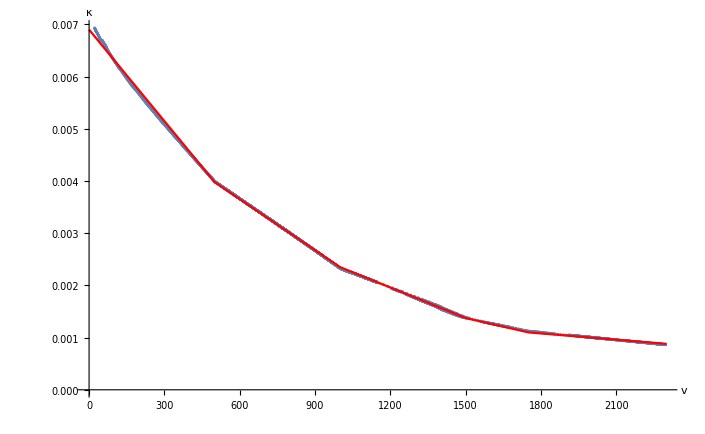

```mathematica
Show[
ListPlot[Transpose[{vf, ω/vf}], AxesLabel->{"v", "κ"}],
Plot[κ[x], {x, 0, 2300}, PlotStyle->Red]
]
```